# Thredshold Ver.3

#### 1. alpha, beta 的值很重要，只要變動一點相圖就會不一樣，所以要去看原先的那篇paper 2. 改變I，Iimit cycle不是往外擴張，而是會平移變形(用Fizhugh-Nagumo model就很好想像) 3. thresold受到很多細節調控，在這個code裡以I2和dI作為變因，但像alpha, beta那些的參數也會影響到，別小看 4D nonlinear model 的威力(所以在我們連正常訊號都搞不懂的情況下就別再想+雜訊啦~) 4. 可以試試”_/-“，看看會不會有變化 5. 剩下的就是把相圖完成了~ 6. The amplitude of spikes is not a constant. There are two possible reason: (1) numerical error (2) chaos phenomenon due to 4 dimentional nonlinear system 7. S.R 之間是虛線, which means that these two area do not have robust difference( or definition) between them. 8. Be careful, do not make the conclusions with only a few spike!

# Constants of HHmodel

```mathematica
ClearAll;
Clear[Cm]
Clear[ gNa, gK, gL]
Clear[ ENa, EK, EL]
Cm=1.0;
(*membrane capacitance, in uF/cm^2*)

gNa=150.0;
(*Sodium [Na] maximum conductances, in mS/cm^2*)

gK=36.0;
(*Postassium [K] maximum conductances, in mS/cm^2*)

gL=0.3;
(*Leak maximum conductances, in mS/cm^2*)

ENa=50.0;
(*Sodium [Na] Nernst reversal potentials, in mV*)

EK=-77.0;
(*Postassium [K] Nernst reversal potentials, in mV*)

EL=-54.387;
(*Leak Nernst reversal potentials, in mV*)
```

```mathematica
Clear[alpham, betam]
Clear[alphah, betah]
Clear[alphan, betan]
Clear[INa, IK, IL, Itot]

alpham[V_]:=0.1 (V+40.0)/(1.0-Exp[-(V+40.0)/10.0])

betam[V_]:= 4.0 Exp[-(V+65.0)/18.0]

alphah[V_]:=0.07 Exp[-(V+65.0)/20.0]

betah[V_]:= 1.0/(1.0+Exp[-(V+35.0)/10.0])

alphan[V_]:=0.01 (V+55.0)/(1.0-Exp[-(V+55.0)/10.0])

betan[V_]:=0.125 Exp[-(V+65)/80.0]

INa[V_,m_,h_]:=gNa (m^3) h (V-ENa)

IK[V_,n_]:=gK (n^4) (V-EK)

IL[V_]:=gL (V-EL);

Itot = INa+IK+IL;
```

# Observing the theshold by changing dI and I2

```mathematica
Clear[data]
data = {};
```

```mathematica
Clear [dI, I1, I2, dtime,linj]

dtime = 100;
Iinj[t_,I10_,dI0_]:= I10 HeavisideTheta[t + 1] + dI0 HeavisideTheta[t - dtime];
(*TaV=Table[,{i,Length@}]*)
For [I2 = 0, I2 < 1.2, I2+=0.05;
 For[dI = 1.4, dI < 1.8, dI+=0.05;

	(*I2 = -2;
	dI = 0;*)

	I1 = I2 - dI;

	(*Block[{hh,TaV,V,m,h,n,V0,MTaV,Vpeak},*)
  (*"t+1"是為了避開0點沒有定義*)
	Block[{hh,TaV,MTaV,V0,Vpeak},
	hh = NDSolve[{
		V'[t] == (Iinj[t,I1,dI] - INa[V[t], m[t], h[t]] - IK[V[t], n[t]] - IL[V[t]])/Cm,
		m'[t] == alpham[V[t]]*(1.0 - m[t]) - betam[V[t]] m[t],
		h'[t] == alphah[V[t]]*(1.0 - h[t]) - betah[V[t]] h[t], 
		n'[t] == alphan[V[t]]*(1.0 - n[t]) - betan[V[t]] n[t],
		V[0] == -65, m[0] == 0.05, n[0] == 0.32, h[0] == 0.6},
		{V, m, h, n}, {t, 0, 500},MaxSteps->10^6];

	(*先把函數descritize得到一個陣列*)
	TaV=Table[{t,(V[t]/.hh)⟦1⟧},{t,100,500,0.01}];
	(*取得另一個陣列 V[t]*V[t+0.01]*)
	(*這個陣列大部份的第二項都是正的 只有在 V[t]~0附近是負的*)
	MTaV=Table[{TaV⟦i,1⟧,TaV⟦i,2⟧ TaV⟦i+1,2⟧},{i,Length@TaV-1}];
	(*把function 切在V=0那邊*)
	(*得到所有的V[t]=0的t*)
	V0=Select[MTaV,#⟦2⟧<0&];
	(*把相鄰的兩個V[t]=0取平均就大約是peak值的時間了*)
	Vpeak=Table[(V0⟦i,1⟧+V0⟦i+1,1⟧)/2,{i,1,Length@V0-1,2}];

	data=Append[data,{I2,dI,Length@Vpeak}];
	]
]]
```

```mathematica
data
```

{{1,1,0},{1,2,1},{1,3,1},{1,4,1},{2,1,0},{2,2,1},{2,3,1},{2,4,1},{3,1,0},{3,2,21},{3,3,21},{3,4,21},{4,1,23},{4,2,23},{4,3,23},{4,4,23}}

```mathematica
ListPlot3D[data,Mesh->All]
ListPlot3D[data,Mesh->None,InterpolationOrder->0,ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

-Graphics3D-

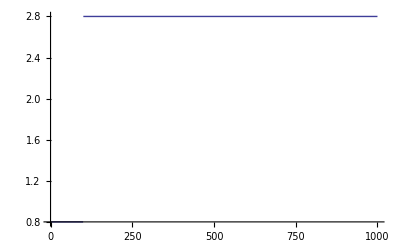

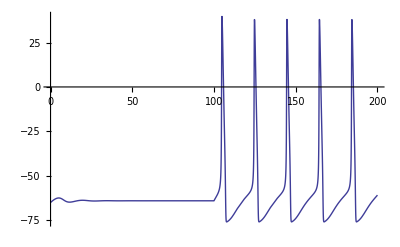

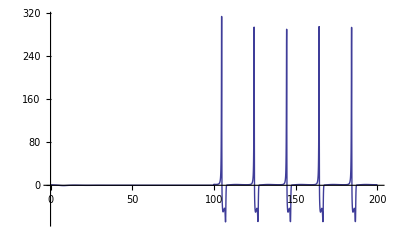

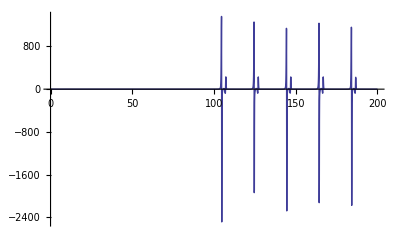

```mathematica
Plot[Iinj[t],{t,0,1000}]
Plot[V[t]/.hh,{t,0,200},PlotRange->All]
Plot[V'[t]/.hh,{t,0,200},PlotRange->All]
Plot[V''[t]/.hh,{t,0,200},PlotRange->All]
```

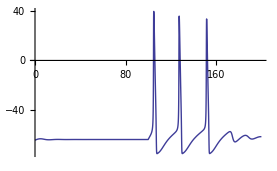
```mathematica
-Graphics-(*I2=2.39,dI=2.1)
```

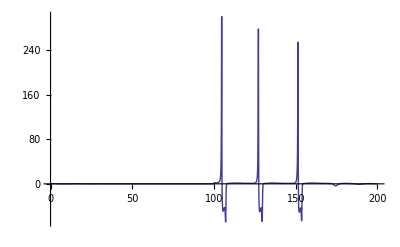

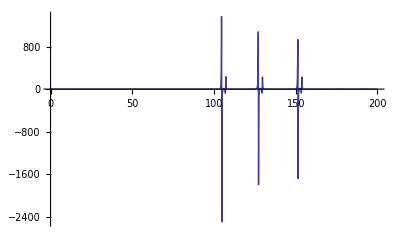

#### 1. Hyerpolarization can induce neuron to detect subthredshold signal. 2. 些微變動會讓原本可fire的神經不fire 3. stochastic的效應是主要是增加dI?! 4. 在0附近的一定區間內是會fire的(以I2=2.5為例，dI=0.05對fire pattern幾乎沒有影響) 5. 一言以蔽之，就是limit cycle 和 stable point在競爭 -Graphics-

# Collect the peaks

```mathematica
data={};
dtime = 100;
Iinj[t_,I10_,dI0_]:= I10 HeavisideTheta[t + 1] + dI0 HeavisideTheta[t - dtime];
I2 = 3.39;
	dI = 1;

	I1 = I2 - dI;

	Block[{hh,TaV,V0,MTaV,Vpeak},
  (*"t+1"是為了避開0點沒有定義*)

	hh = NDSolve[{
		V'[t] == (Iinj[t,I1,dI] - INa[V[t], m[t], h[t]] - IK[V[t], n[t]] - IL[V[t]])/Cm,
		m'[t] == alpham[V[t]]*(1.0 - m[t]) - betam[V[t]] m[t],
		h'[t] == alphah[V[t]]*(1.0 - h[t]) - betah[V[t]] h[t], 
		n'[t] == alphan[V[t]]*(1.0 - n[t]) - betan[V[t]] n[t],
		V[0] == -65, m[0] == 0.05, n[0] == 0.32, h[0] == 0.6},
		{V, m, h, n}, {t, 0, 500},MaxSteps->10^6];

	(*先把函數descritize得到一個陣列*)
	TaV=Table[{t,(V[t]/.hh)⟦1⟧},{t,100,500,0.01}]
	(*取得另一個陣列 V[t]*V[t+0.01]*)
	(*這個陣列大部份的第二項都是正的 只有在 V[t]~0附近是負的*)
	MTaV=Table[{TaV⟦i,1⟧,TaV⟦i,2⟧ TaV⟦i+1,2⟧},{i,Length@TaV-1}]
	(*把function 切在V=0那邊*)
	(*得到所有的V[t]=0的t*)
	V0=Select[MTaV,#⟦2⟧<0&]
	(*把相鄰的兩個V[t]=0取平均就大約是peak值的時間了*)
	Vpeak=Table[(V0⟦i,1⟧+V0⟦i+1,1⟧)/2,{i,1,Length@V0-1,2}]

	data=Append[data,{I2,dI,Length@Vpeak}]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[MTaV, #1 ⟦ 2 ⟧ < 0 &].

Set::write: Tag Times in {}\ {} is Protected.

Set::write: Tag Times in V0\ {} is Protected.

Set::write: Tag Times in MTaV\ {{100., -62.3107}, {100.01, -62.3029}, {100.02, -62.2952}, {100.03, -62.2876}, {100.04, -62.2801}, {100.05, -62.2727}, {100.06, -62.2653}, {100.07, -62.258}, {100.08, -62.2508}, {100.09, -62.2437}, {100.1, -62.2367}, « 29 », {100.4, -62.0454}, {100.41, -62.0395}, {100.42, -62.0336}, {100.43, -62.0277}, {100.44, -62.0218}, {100.45, -62.0159}, {100.46, -62.0101}, {100.47, -62.0043}, {100.48, -61.9984}, {100.49, -61.9926}, « 39951 »} is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{{},{},0}}

```mathematica
a={}
```

{}

```mathematica
b=Append[a,{2}]
```

{{2}}